# 区间作图与区间的相交

## 区间作图

```mathematica
inters={{31,42},{58,74},{99,120},{122,148},{159,190},{270,311},{319,376},{366,380},{366,390},{380,400},{463,499},{511,556},{548,556},{632,654},{657,678},{687,704},{707,718},{725,732}};
```

```mathematica
IntervalIntersection@@@Select[Partition[Interval/@inters,2,1,1,{}],Length[#]==2&]
```

{Interval[],Interval[],Interval[],Interval[],Interval[],Interval[],Interval[{366,376}],Interval[{366,380}],Interval[{380,390}],Interval[],Interval[],Interval[{548,556}],Interval[],Interval[],Interval[],Interval[],Interval[]}

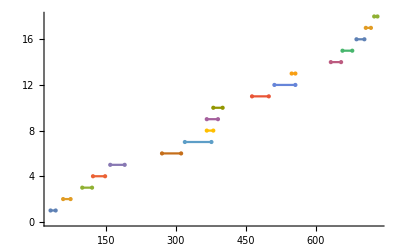

```mathematica
gr=NumberLinePlot[Interval/@inters]
```

## 剔除相交的区间的后一个

### Basic

```mathematica
len=Length@inters;
```

```mathematica
index={};For[i=1,i<len,i++,If[inters[[i]][[2]]>inters[[i+1]][[1]],AppendTo[index,i]]];
index+1
```

{3,4,5,8}

```mathematica
inters[[#]]&/@(index+1)
```

{{366,380},{366,390},{380,400},{548,556}}

### 改进

上面的例子中，3和4剔除后，5是没有必要剔除的。
因此多个连续相交的情形要改进下，剔除后自然也是没有相交的区间。

```mathematica
len=Length@inters;
index={};j=1;
(*j为要删除元素的前一个的索引号*)
For[i=1,i<len,i++,If[inters[[i+1]][[1]]<=inters[[j]][[2]],Print["i="<>ToString[i]];Print["True j="<>ToString[j]];AppendTo[index,i+1];,j=i+1;Print["i="<>ToString[i]]]];
index
inters[[#]]&/@(index)
```

i=1

i=2

True j=2

i=3

True j=2

i=4

i=5

i=6

i=7

True j=7

i=8

i=9

i=10

i=11

i=12

{3,4,8}

{{366,380},{366,390},{548,556}}

可以看到改进版少剔除了一个数，符合预期。

## 总结

此方法至少在两个场景相关会遇到
一个是StringReplacePart时的Overlapping问题，还有一个是比如时间戳是按时间间隔剔除的情形。

```mathematica
Notebook2GitHubPage[EvaluationNotebook[]]
```